```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={x>0};
```

```mathematica
n=10
```

10

```mathematica
X[x_]:={x,x}
```

```mathematica
ν[x_]:=FullSimplify[Norm[X'[x]],Assumptions->ass]
```

```mathematica
ψ[x_]:=FullSimplify[ArcTan[X'[x][[1]],-X'[x][[2]]],Assumptions->ass]
```

```mathematica
v[x_]:=1
```

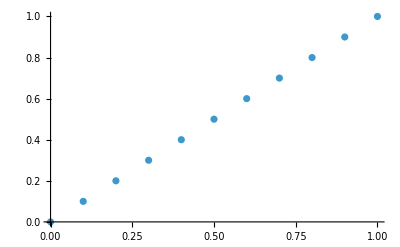

```mathematica
ListPlot[Table[X[i/n],{i,0,n}]]
```

```mathematica
(*write X*)
```

```mathematica
t=Table[{X[i/n][[1]], X[i/n][[2]],0,i/n,0,0},{i,0,n}]//N
```

{{0.,0.,0.,0.,0.,0.},{0.1,0.1,0.,0.1,0.,0.},{0.2,0.2,0.,0.2,0.,0.},{0.3,0.3,0.,0.3,0.,0.},{0.4,0.4,0.,0.4,0.,0.},{0.5,0.5,0.,0.5,0.,0.},{0.6,0.6,0.,0.6,0.,0.},{0.7,0.7,0.,0.7,0.,0.},{0.8,0.8,0.,0.8,0.,0.},{0.9,0.9,0.,0.9,0.,0.},{1.,1.,0.,1.,0.,0.}}

```mathematica
PrependTo[t,{"f:0","f:1","f:2",":0",":1",":2"}]
```

{{f:0,f:1,f:2,:0,:1,:2},{0.,0.,0.,0.,0.,0.},{0.1,0.1,0.,0.1,0.,0.},{0.2,0.2,0.,0.2,0.,0.},{0.3,0.3,0.,0.3,0.,0.},{0.4,0.4,0.,0.4,0.,0.},{0.5,0.5,0.,0.5,0.,0.},{0.6,0.6,0.,0.6,0.,0.},{0.7,0.7,0.,0.7,0.,0.},{0.8,0.8,0.,0.8,0.,0.},{0.9,0.9,0.,0.9,0.,0.},{1.,1.,0.,1.,0.,0.}}

```mathematica
Export["/Users/michelecastellana/Documents/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/X_n_12_1.csv",t];
```

```mathematica
(*write ν*)
```

```mathematica
t=Table[{ν[i/n],0,i/n,0,0},{i,0,n}]//N
```

{{1.41421,0.,0.,0.,0.},{1.41421,0.,0.1,0.,0.},{1.41421,0.,0.2,0.,0.},{1.41421,0.,0.3,0.,0.},{1.41421,0.,0.4,0.,0.},{1.41421,0.,0.5,0.,0.},{1.41421,0.,0.6,0.,0.},{1.41421,0.,0.7,0.,0.},{1.41421,0.,0.8,0.,0.},{1.41421,0.,0.9,0.,0.},{1.41421,0.,1.,0.,0.}}

```mathematica
PrependTo[t,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{1.41421,0.,0.,0.,0.},{1.41421,0.,0.1,0.,0.},{1.41421,0.,0.2,0.,0.},{1.41421,0.,0.3,0.,0.},{1.41421,0.,0.4,0.,0.},{1.41421,0.,0.5,0.,0.},{1.41421,0.,0.6,0.,0.},{1.41421,0.,0.7,0.,0.},{1.41421,0.,0.8,0.,0.},{1.41421,0.,0.9,0.,0.},{1.41421,0.,1.,0.,0.}}

```mathematica
Export["/Users/michelecastellana/Documents/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/nu_n_12_1.csv",t];
```

```mathematica
(*write ψ*)
```

```mathematica
t=Table[{ψ[i/n],0,i/n,0,0},{i,0,n}]//N
```

{{-0.785398,0.,0.,0.,0.},{-0.785398,0.,0.1,0.,0.},{-0.785398,0.,0.2,0.,0.},{-0.785398,0.,0.3,0.,0.},{-0.785398,0.,0.4,0.,0.},{-0.785398,0.,0.5,0.,0.},{-0.785398,0.,0.6,0.,0.},{-0.785398,0.,0.7,0.,0.},{-0.785398,0.,0.8,0.,0.},{-0.785398,0.,0.9,0.,0.},{-0.785398,0.,1.,0.,0.}}

```mathematica
PrependTo[t,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{-0.785398,0.,0.,0.,0.},{-0.785398,0.,0.1,0.,0.},{-0.785398,0.,0.2,0.,0.},{-0.785398,0.,0.3,0.,0.},{-0.785398,0.,0.4,0.,0.},{-0.785398,0.,0.5,0.,0.},{-0.785398,0.,0.6,0.,0.},{-0.785398,0.,0.7,0.,0.},{-0.785398,0.,0.8,0.,0.},{-0.785398,0.,0.9,0.,0.},{-0.785398,0.,1.,0.,0.}}

```mathematica
Export["/Users/michelecastellana/Documents/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/psi_n_12_1.csv",t];
```

```mathematica
(*write v*)
```

```mathematica
t=Table[{v[i/n],0,0,i/n,0,0},{i,0,n}]//N
```

{{1.,0.,0.,0.,0.,0.},{1.,0.,0.,0.1,0.,0.},{1.,0.,0.,0.2,0.,0.},{1.,0.,0.,0.3,0.,0.},{1.,0.,0.,0.4,0.,0.},{1.,0.,0.,0.5,0.,0.},{1.,0.,0.,0.6,0.,0.},{1.,0.,0.,0.7,0.,0.},{1.,0.,0.,0.8,0.,0.},{1.,0.,0.,0.9,0.,0.},{1.,0.,0.,1.,0.,0.}}

```mathematica
PrependTo[t,{"f:0","f:1","f:2",":0",":1",":2"}]
```

{{f:0,f:1,f:2,:0,:1,:2},{1.,0.,0.,0.,0.,0.},{1.,0.,0.,0.1,0.,0.},{1.,0.,0.,0.2,0.,0.},{1.,0.,0.,0.3,0.,0.},{1.,0.,0.,0.4,0.,0.},{1.,0.,0.,0.5,0.,0.},{1.,0.,0.,0.6,0.,0.},{1.,0.,0.,0.7,0.,0.},{1.,0.,0.,0.8,0.,0.},{1.,0.,0.,0.9,0.,0.},{1.,0.,0.,1.,0.,0.}}

```mathematica
Export["/Users/michelecastellana/Documents/paper_ale/figures/figure_4/solution/snapshots/csv/nodal_values/v_n_1.csv",t];
```